This is an early, quick-and-dirty attempt to write a two-dimensional N-body simulator.  It solves NSL exactly, and uses cartesian coördinates.

```mathematica
ClearAll["Global`*"]
```

```mathematica
<<"/Users/alexdeich/thesis/code/mine/ThesisTools.m"
```

#### Initilialize potentially useful things

Initialize state vector with {{m},{x,y},{xd,yd}}

```mathematica
(*InitVecs = Table[{{RandomReal[{-2,2}],RandomReal[{-2,2}]},{0,RandomReal[{-0.5,0.5}]}},Nparticles];*)
timesteps = 20000;
dt = .00001;
mass = 10;
epsilon = 0.0001;
InitVecs = {{{1000},{0,0},{0,0}},{{.001},{0.,200.1},{5,0}},{{1.},{0.,200.},{2.,0.}},{{1.},{100.,0.},{0.,-3.}}};
wholestory = Table[0,timesteps];
Nparticles = Length[InitVecs];
```

```mathematica
InitVecs[[2,1,1]]
```

1

#### Calculate force on one particle due to all the others

SingleParticleForce[f_,i_] returns the force on the particle i whose position in state space is given in f , which is an array (created above as InitVecs.)

```mathematica
SingleParticleForce[f_,i_]:=Module[{j,x1,x2,y1,y2,m1,m2,distance2,jforce,jforcedir,totalforce,forces},
forces = Table[{0.,0.},Nparticles];
x1 = f[[i,2,1]];
y1 = f[[i,2,2]];
m1 = f[[i,1,1]];
For [j=1,j≤ Nparticles,j++,
If[j≠ i,
m2 = f[[j,1,1]];
x2 = f[[j,2,1]];
y2 = f[[j,2,2]];
distance2 = ((x2-x1)^2+(y2-y1)^2);
jforce = (m2)/distance2;
jforcedir = {x2-x1,y2-y1}/Sqrt[distance2];
forces[[j]] = jforce*jforcedir;
];
];
Return[Total[forces]];
]
```

```mathematica
SingleParticleForce[InitVecs,1]
```

{0.,-0.277633}

#### Get force on every particle

GetForces[state_] returns an array with size Nparticles with the force information for each particle in x and y: {{fx},{fy}}

```mathematica
GetForces[state_]:=Module[{particle,totalforces},
totalforces = Table[{},Nparticles];
For[particle=1,particle≤Nparticles,particle++,
totalforces[[particle]]=SingleParticleForce[state,particle]
];
Return[totalforces]
]
```

For a sanity check, if Nparticles==2, the two forces returned should be equal and opposite.

```mathematica
GetForces[InitVecs]
```

{{0.00444444,0.0025},{0.00096,-0.25128},{-0.445404,0.00128}}

#### Time evolution

```mathematica
StateVecs = InitVecs;
For[timestep = 1,timestep≤timesteps,timestep++,
currentforces = GetForces[StateVecs];
NewState = Table[{{0},{0,0},{0,0}},Nparticles];
For[i=1,i≤ Nparticles,i++,
oldx = StateVecs[[i,2,1]];
oldy = StateVecs[[i,2,2]];
oldxd = StateVecs[[i,3,1]];
oldyd = StateVecs[[i,3,2]];
xdd= currentforces[[i,1]];
ydd = currentforces[[i,2]];
newx = oldxd * dt + oldx;
newy = oldyd * dt + oldy;
newxd = xdd*dt + oldxd;
newyd = ydd*dt + oldyd;
m = StateVecs[[i,1,1]];
NewState[[i,1,1]] = m;
NewState[[i,2,1]] = newx;
NewState[[i,2,2]] = newy;
NewState[[i,3,1]] = newxd;
NewState[[i,3,2]] = newyd;
];
StateVecs = NewState;
(*Print[timestep," ",StateVecs];*)
wholestory[[timestep]] = StateVecs;
]
```

```mathematica
Dynamic[timestep]
```

#### Plotting

```mathematica
colors = {Blue,Red,Black,Orange,Green};
```

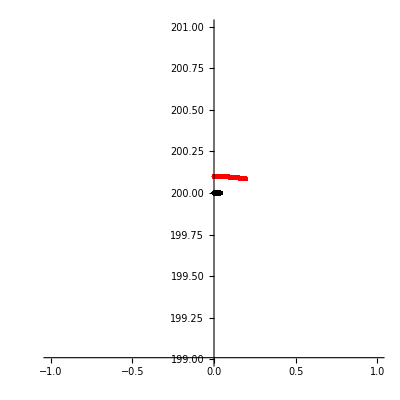

```mathematica
xyplots = Table[0,Nparticles];
plotrange = 210;
For[particle=1,particle≤Nparticles,particle++,
xyplots[[particle]] = ListPlot[Table[{wholestory[[t,particle,2,1]],wholestory[[t,particle,2,2]]},{t,1,timesteps}],PlotRange->{{-1,1},{199,201}},PlotStyle->{colors[[particle]],PointSize[Medium]},AspectRatio->1];
]
Show[xyplots]
```

```mathematica
Show[xyplots]
```

Show::gcomb: Could not combine the graphics objects in Show[{,,0,0}].

Show[{-Graphics-,-Graphics-,0,0}]

#### To do

• Track masses? it isn’t necessary for the final thing, but it would be cool
• Optimize, allow for collisions, particle clumping
• How to combine with Kerr RK4?!?!?!?
	-Maybe rewrite this so that it uses RK4, too.  This will not be a straightforward adaptation of the Kerr RK4 example, because you need to recalculate the derivative vector (G[x,f] in the Kerr example) at every time step.